## Preliminary System Setup

```mathematica
(*Define rate of change of sunflower population*)
dsdt[s_,z_, β_, γ_, s∞_] := β s(1 - s/(s∞)) - γ s z
(*Define rate of change of zombie population*)
dzdt[s_,z_, δ_, γ_] := - δ z + 4γ s z
```

```mathematica
(*Initialise functions to show points on the graph*)
whiteDot=xx↦{Black,PointSize[0.02], Point[xx],White,PointSize[0.015],Point[xx]};
blackDot=xx↦{Black,PointSize[0.02], Point[xx]};
yellowDot = xx ↦ {Yellow, PointSize[0.02], Point[xx]};
```

## Generating Phase Space Diagram

```mathematica
Manipulate[StreamPlot[{dsdt[s, z, β, γ, s∞], dzdt[s, z, δ, γ]}, {s, -1,100}, {z, -1, 100}, 
(*Styling*)
StreamStyle->Arrowheads[Small], StreamPoints->Fine,AxesLabel->{"s", "z"}, Frame -> True , PlotRangePadding->None, FrameLabel -> {"Sunflowers (S)", "Zombies (Z)"},

(*Plot a black dot at stable equilibria, yellow at saddles, white dot at unstable.
This dynamically updates as parameters are changed.*)
Epilog -> {blackDot[{δ/(4γ), β/γ*(1 - δ/(4*γ*s∞))}],yellowDot[{0,0}], 
If[δ/(4γ)<s∞,yellowDot[{s∞, 0}],blackDot[{s∞,0}]]}], 
{{β, 0.5}, 0, 2} (*Define sunflower plant rate β*), 
{{γ, 0.01}, 0.001, 2} (*Define predation rate γ*),
{{δ, 0.25}, 0, 0.40} (*Define zombie death rate δ*), 
{{s∞, 90}, 0.001, 100}(*Define sunflower carrying capacity*)
(*Interesting behaviour as 4γs∞ < δ, stable spiral crosses saddle and saddle changes into stable node.*)
]
```

## Plotting Bifurcation Behaviour

```mathematica
(*Plot eigenvalues, prove safety in preliminary model.*)
Manipulate[
(*Define bifurcation points and eigenvalues, to show meaningful relationships.*)
Module[
{
bifurcationPoint=δ/(4 γ)
},

(*Coexistence point, zombie population, limit equilibrium*)
Zcoex[s∞_]:= 64 *s∞^2*γ^2 - 16 s∞ γ δ - β δ;
Z[s∞_]:=β/γ (1-δ/(4 γ s∞));
Zlim[s∞_] := 4γ s∞ - δ;

(*Plot respective graphs*)
Show[
Plot[If[Z[s∞] >0,Z[s∞], None],
{s∞, -20, 200},
PlotStyle -> {Thick, Blue},
PlotRange -> {-10, 40},
AxesOrigin -> {0,0}, Frame -> True , PlotRangePadding->None, FrameLabel -> {"Carrying Capacity (s∞)", "Zombies (Blue), Eigenvalues (Red, Black)"}
],

Plot[If[Z[s∞] < 0,Z[s∞], None],
{s∞, -100, 200},
PlotStyle -> {Dashed, Blue},
PlotRange -> {-100, 200},
AxesOrigin -> {0,0}
],

Plot[If[Zcoex[s∞] > 0,Zcoex[s∞], None],
{s∞, -100, 200},
PlotStyle -> {Thick, Red},
PlotRange -> {-100, 200},
AxesOrigin -> {0,0}
],


Plot[If[Zcoex[s∞] < 0,Zcoex[s∞], None],
{s∞, -100, 200},
PlotStyle -> {Dashed, Red},
PlotRange -> {-100, 200},
AxesOrigin -> {0,0}
],

Plot[If[Zlim[s∞] < 0,Zlim[s∞], None],
{s∞, -100, 200},
PlotStyle -> {Thick, Black},
PlotRange -> {-100, 200},
AxesOrigin -> {0,0}
],

Plot[If[Zlim[s∞] > 0,Zlim[s∞], None],
{s∞, -100, 200},
PlotStyle -> {Dashed, Black},
PlotRange -> {-100, 200},
AxesOrigin -> {0,0}
],

(*Show bifurcation point*)
Epilog -> blackDot[{bifurcationPoint,0}]
]],
{{β, 0.5}, 0.01, 2},
{{γ, 0.001}, 0.001, 0.01},
{{δ, 0.25}, 0.2, 0.4}

]
```

## Solving Using RKF45

```mathematica
(*Loading RKF45 Solver from Freddie Page's Lectures*)
rkf45=Module[{rkf45prime,β,α,c,cHat,cT},
β=N[{{2/9, 0, 0, 0, 0}, {1/12, 1/4, 0, 0, 0}, {69/128, -243/128, 135/64, 0, 0}, {-17/12, 27/4, -27/5, 16/15, 0}, {65/432, -5/16, 13/16, 4/27, 5/144}}];
α=Total/@β;
c={1/9,0,9/20,16/45,1/12,0};
cHat={47/450,0,12/25,32/225,1/30,6/25};
cT=cHat-c;
rkf45prime={f,tol}↦Apply[{t,x,h}↦Module[
{f0,f1,f2,f3,f4,f5,xNext,xHat,hNext,TE},
f0=f[t,x];
f1=f[t+α⟦1⟧h,x+h(β⟦1,1⟧ f0)];
f2=f[t+α⟦2⟧h,x+h(β⟦2,1⟧ f0+β⟦2,2⟧ f1)];
f3=f[t+α⟦3⟧h,x+h(β⟦3,1⟧ f0+β⟦3,2⟧ f1+β⟦3,3⟧ f2)];
f4=f[t+α⟦4⟧h,x+h(β⟦4,1⟧ f0+β⟦4,2⟧ f1+β⟦4,3⟧ f2+β⟦4,4⟧ f3)];
f5=f[t+α⟦5⟧h,x+h(β⟦5,1⟧ f0+β⟦5,2⟧ f1+β⟦5,3⟧ f2+β⟦5,4⟧ f3+β⟦5,5⟧ f3)];
xNext=x+h(c⟦1⟧f0+c⟦2⟧f1+c⟦3⟧f2+c⟦4⟧f3+c⟦5⟧f4);
xHat=x+h(cHat⟦1⟧f0+cHat⟦2⟧f1+cHat⟦3⟧f2+cHat⟦4⟧f3+cHat⟦5⟧f4+cHat⟦6⟧f5);
TE=h(cT⟦1⟧f0+cT⟦2⟧f1+cT⟦3⟧f2+cT⟦4⟧f3+cT⟦5⟧f4+cT⟦6⟧f5);
hNext=0.9 h(tol/Max[Abs[TE]])^(1/5);
If[
Max[Abs[TE]]>tol,
{t,x,hNext,True},
{t+h,xHat,hNext,False}
]
]];
{f,tol}↦Module[{
stepPrime=rkf45prime[{t,x}↦f[t,Sequence@@x],tol]
},
Apply[{t,x,h}↦Most@NestWhile[stepPrime,{t,x,h,True},#⟦4⟧&]]
]
];
```

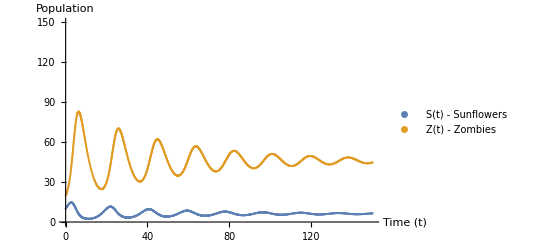

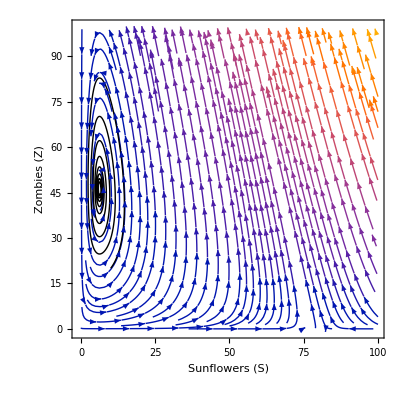

```mathematica
(*Define the system of equations f*)
f={β,γ,δ,s∞}|->{t,x,y}|->{β x (1-x/s∞)-γ x y,4 γ x y-δ y};

(*Define initial parameter values and conditions. Tried making this interactive, but it was
massively laggy and crashed my Mathematica a few times even with higher error tol. Manually changing would be better.*)
β = 0.5;
γ = 0.01;
δ = 0.25;
s∞ = 80;
initialConditions = {0, {10, 20}, 0.1};
tol = 10^-6;

(*Input into RKF solver*)
update = rkf45[f[β, γ, δ, s∞], tol];

data = NestWhileList[update, initialConditions,#[[1]]<150&];
Transpose[(s↦{{s[[1]],s[[2,1]]},{s[[1]],s[[2,2]]}})/@%];
ListPlot[%,PlotRange->{0,150}, PlotLegends->{"S(t) - Sunflowers","Z(t) - Zombies"}, AxesLabel -> {"Time (t)", "Population"}]

(*Mapping trajectories onto the streamplot. First step is defining streamplot.*)
vectorField = StreamPlot[{dsdt[s, z, β, γ, s∞], dzdt[s, z, δ, γ]}, {s, -1,100}, {z, -1, 100}, 
(*Styling*)
StreamStyle->Arrowheads[Small], StreamPoints->Fine,AxesLabel->{"s", "z"}, Frame -> True , PlotRangePadding->None, FrameLabel -> {"Sunflowers (S)", "Zombies (Z)"}];

(*Create Line with coordinates = S population, Z population. *)
trajectory = data[[All, 2]];
trajectoryLine = Graphics[{Black, Thick, Line[trajectory]}];

(*Overlay maps*)
Show[vectorField, trajectoryLine]
```

## Generating Ensemble Simulations

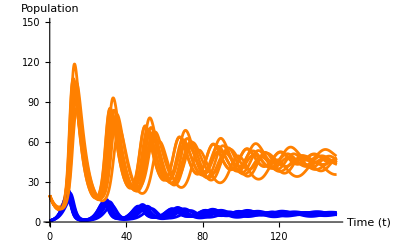

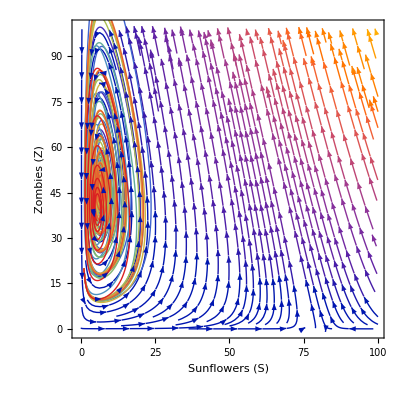

```mathematica
(*Baseline Parameters*)
baselineParams={β->0.5,γ->0.01,δ->0.25,s∞->80};

(*Controls the magnitude of perturbations. Other conditions are redefined here for ease of editing.
Tolerance slightly slackened for computing time*)
pertStr=0.1;
numSimulations=10;
initialConditions={0,{1,20},0.1};
tol=10^-5;

(*Define the system of equations*)
f={β,γ,δ,s∞}|->{t,x,y}|->{β x (1-x/s∞)-γ x y,4 γ x y-δ y};

(*Store all trajectories and time series data*)
SolutionData=Table[
Module[
{β,γ,δ,s∞,update,data,solution},(*Perturb parameters by a percentage pertStr*)
β=baselineParams[[1,2]]*(1+RandomReal[{-pertStr,pertStr}]);
γ=baselineParams[[2,2]]*(1+RandomReal[{-pertStr,pertStr}]);
δ=baselineParams[[3,2]]*(1+RandomReal[{-pertStr,pertStr}]);
s∞=baselineParams[[4,2]]*(1+RandomReal[{-pertStr,pertStr}]);

(*RKF solver*)
update=rkf45[f[β,γ,δ,s∞],tol];
solution=NestWhileList[update,initialConditions,#[[1]]<150&];

(*Process the solution into time-series data*)
data=Transpose[{solution[[All,1]],(*Time values*)
solution[[All,2,1]],(*S(t) values*)
solution[[All,2,2]]  (*Z(t) values*)}];

(*Create Time Series Plots*)
{ListLinePlot[{data[[All,{1,2}]],(*S(t) vs Time*)
data[[All,{1,3}]]},(*Z(t) vs Time*)
PlotStyle->{Blue,Orange},AxesLabel->{"Time (t)","Population"},PlotRange->{0,150}],

(*Collect Trajectory Data*)
Line[Transpose[{data[[All,2]],data[[All,3]]}]] (*Phase space trajectory*)}],

(*Repeat numSimulation times*)
{i,numSimulations}];

(*Extract time series plots and trajectories*)
TimeSeriesPlot=SolutionData[[All,1]];
Trajectories=SolutionData[[All,2]];

(*Combine all trajectories into a single Graphics object*)
allTrajectoryLines=Graphics[Table[{ColorData["Rainbow"][i/numSimulations],Thick,Trajectories[[i]]},{i,numSimulations}]];

(*Combine all time series plots into one visualization*)
Show[TimeSeriesPlot]

(*Overlay the vector field with the trajectories*)
Show[vectorField,allTrajectoryLines]
```

## Second Iteration Numerical Solution

```mathematica
(*Loading RKF45 Solver from Freddie Page's Lectures, modified to not unpack f input.*)
rkf45=Module[{rkf45prime,β,α,c,cHat,cT},
β=N[{{2/9, 0, 0, 0, 0}, {1/12, 1/4, 0, 0, 0}, {69/128, -243/128, 135/64, 0, 0}, {-17/12, 27/4, -27/5, 16/15, 0}, {65/432, -5/16, 13/16, 4/27, 5/144}}];
α=Total/@β;
c={1/9,0,9/20,16/45,1/12,0};
cHat={47/450,0,12/25,32/225,1/30,6/25};
cT=cHat-c;
rkf45prime={f,tol}↦Apply[{t,x,h}↦Module[
{f0,f1,f2,f3,f4,f5,xNext,xHat,hNext,TE},
f0=f[t,x];
f1=f[t+α⟦1⟧h,x+h(β⟦1,1⟧ f0)];
f2=f[t+α⟦2⟧h,x+h(β⟦2,1⟧ f0+β⟦2,2⟧ f1)];
f3=f[t+α⟦3⟧h,x+h(β⟦3,1⟧ f0+β⟦3,2⟧ f1+β⟦3,3⟧ f2)];
f4=f[t+α⟦4⟧h,x+h(β⟦4,1⟧ f0+β⟦4,2⟧ f1+β⟦4,3⟧ f2+β⟦4,4⟧ f3)];
f5=f[t+α⟦5⟧h,x+h(β⟦5,1⟧ f0+β⟦5,2⟧ f1+β⟦5,3⟧ f2+β⟦5,4⟧ f3+β⟦5,5⟧ f3)];
xNext=x+h(c⟦1⟧f0+c⟦2⟧f1+c⟦3⟧f2+c⟦4⟧f3+c⟦5⟧f4);
xHat=x+h(cHat⟦1⟧f0+cHat⟦2⟧f1+cHat⟦3⟧f2+cHat⟦4⟧f3+cHat⟦5⟧f4+cHat⟦6⟧f5);
TE=h(cT⟦1⟧f0+cT⟦2⟧f1+cT⟦3⟧f2+cT⟦4⟧f3+cT⟦5⟧f4+cT⟦6⟧f5);
hNext=0.9 h(tol/Max[Abs[TE]])^(1/5);
If[
Max[Abs[TE]]>tol,
{t,x,hNext,True},
{t+h,xHat,hNext,False}
]
]];
{f,tol}↦Module[{
stepPrime=rkf45prime[{t,x}↦f[t,x],tol]
},
Apply[{t,x,h}↦Most@NestWhile[stepPrime,{t,x,h,True},#⟦4⟧&]]
]
];
```

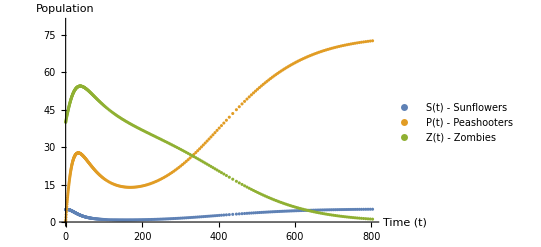

```mathematica
(*Defining new functions, with variables as a state vector for rkf compatibility*)
f={α,β,γ,δ,s∞}|->{t,x}|->
{α β x[[1]] (1-(x[[1]]+x[[2]])/s∞)-γ x[[1]] x[[3]],β x[[1]] (1-α/2) (1-(x[[1]]+x[[2]])/s∞)-(1-δ) γ x[[2]] x[[3]],4 γ x[[1]] x[[3]]-δ γ x[[2]] x[[3]]};

(*Define parameters and initial conditions*)
α=0.1;
β=0.5;
γ=0.001;
δ=0.4;
s∞=80;
initialConditions={0,{5,0,40},0.1};
tol=10^-6;

(*Input into RKF solver*)
update=rkf45[f[α,β,γ,δ,s∞],tol];
data = NestWhileList[update, initialConditions,#[[1]]<800&];
Transpose[(s↦{{s[[1]],s[[2,1]]},{s[[1]],s[[2,2]]}, {s[[1]], s[[2, 3]]}})/@%];
ListPlot[%,PlotRange->{0,80}, PlotLegends->{"S(t) - Sunflowers","P(t) - Peashooters","Z(t) - Zombies"}, AxesLabel -> {"Time (t)", "Population"}]
```

## Second Iteration Parametric Ensemble

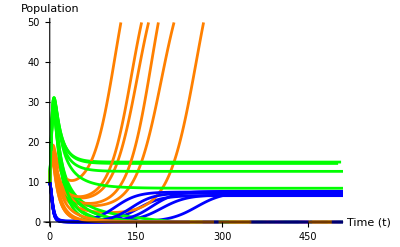

```mathematica
(*Baseline Parameters*)
baselineParams={α->0.1,β->0.5,γ->0.01,δ->0.65,s∞->80};

(*Controls the magnitude of perturbations*)
pertStr=0.1;
numSimulations=10;
initialConditions={0,{10,10,10},0.1};
tol=10^-5;

(*Define the system of equations*)
f={α,β,γ,δ,s∞}|->{t,x}|->
{α β x[[1]] (1-(x[[1]]+x[[2]])/s∞)-γ x[[1]] x[[3]],(*dS/dt*)
β x[[1]] (1-α/2) (1-(x[[1]]+x[[2]])/s∞)-(1-δ) γ x[[2]] x[[3]],(*dP/dt*)
4 γ x[[1]] x[[3]]-δ γ x[[2]] x[[3]] (*dZ/dt*)};

(*Store all trajectories and time series data*)
SolutionData=Table[Module[{α,β,γ,δ,s∞,update,data,solution},
(*Perturb parameters by a percentage pertStr*)
α=baselineParams[[1,2]]*(1+RandomReal[{-pertStr,pertStr}]);
β=baselineParams[[2,2]]*(1+RandomReal[{-pertStr,pertStr}]);
γ=baselineParams[[3,2]]*(1+RandomReal[{-pertStr,pertStr}]);
δ=baselineParams[[4,2]]*(1+RandomReal[{-pertStr,pertStr}]);
s∞=baselineParams[[5,2]]*(1+RandomReal[{-pertStr,pertStr}]);

(*RKF solver*)
update=rkf45[f[α,β,γ,δ,s∞],tol];
solution=NestWhileList[update,initialConditions,#[[1]]<500&];

(*Process the solution into time-series data*)
data=Transpose[{solution[[All,1]],(*Time values*)
solution[[All,2,1]],(*S(t) values*)
solution[[All,2,2]],(*P(t) values*)
solution[[All,2,3]] (*Z(t) values*)}];

(*Return the time series data and the ListLinePlot*)
{data,ListLinePlot[{data[[All,{1,2}]],(*S(t) vs Time*)
data[[All,{1,3}]],(*P(t) vs Time*)
data[[All,{1,4}]]  (*Z(t) vs Time*)},
PlotStyle->{Blue,Orange,Green},AxesLabel->{"Time (t)","Population"},PlotRange->{{0,500}, {0,50}}]}],

(*Repeat numSimulation times*)
{i,numSimulations}];

(*Extract time series plots*)
TimeSeriesPlots=SolutionData[[All,2]];

(*Combine all time series plots into one visualization*)
Show[TimeSeriesPlots]
```

## Second Iteration Starting Conditions Ensemble

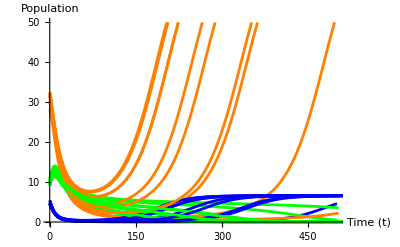

```mathematica
(*Baseline Parameters*)
baselineParams={α->0.1,β->0.5,γ->0.01,δ->0.4,s∞->80};

(*Controls the magnitude of perturbations*)
pertStr=0.1; (*Percentage perturbation*)
numSimulations=10; (*Number of simulations*)
initialConditionsBase={5,30,10}; (*Baseline initial conditions for S,P,Z*)
tol=10^-5;

(*Define the system of equations*)
f={α,β,γ,δ,s∞}|->{t,x}|->
{α β x[[1]] (1-(x[[1]]+x[[2]])/s∞)-γ x[[1]] x[[3]],(*dS/dt*)
β x[[1]] (1-α/2) (1-(x[[1]]+x[[2]])/s∞)-(1-δ) γ x[[2]] x[[3]],(*dP/dt*)
4 γ x[[1]] x[[3]]-δ γ x[[2]] x[[3]] (*dZ/dt*)};

(*Store all trajectories and time series data*)
SolutionData=Table[
Module[{α,β,γ,δ,s∞,update,data,solution,perturbedIC},

(*Use baseline parameters without perturbation*)
{α,β,γ,δ,s∞}=baselineParams[[All,2]];

(*Perturb initial conditions by a percentage pertStr*)perturbedIC=initialConditionsBase*(1+RandomReal[{-pertStr,pertStr},3]);

(*RKF solver*)
update=rkf45[f[α,β,γ,δ,s∞],tol];
solution=NestWhileList[update,{0,perturbedIC,0.1},#[[1]]<500&];

(*Process the solution into time-series data*)
data=Transpose[{solution[[All,1]],(*Time values*)
solution[[All,2,1]],(*S(t) values*)
solution[[All,2,2]],(*P(t) values*)
solution[[All,2,3]]}];(*Z(t) values*)

(*Return the time series data and the ListLinePlot*)
{data,ListLinePlot[{data[[All,{1,2}]],(*S(t) vs Time*)
data[[All,{1,3}]],(*P(t) vs Time*)
data[[All,{1,4}]]  (*Z(t) vs Time*)},

PlotStyle->{Blue,Orange,Green},AxesLabel->{"Time (t)","Population"},PlotRange->{{0,500}, {0, 50}}]}],

(*Repeat numSimulation times*)
{i,numSimulations}];

(*Extract time series plots*)
TimeSeriesPlots=SolutionData[[All,2]];

(*Combine all time series plots into one visualization*)
Show[TimeSeriesPlots]
```

## Second Iteration Vector Plot

```mathematica
(*Define the system of differential equations*)
dsdt[s_, p_, z_, α_,β_,γ_,δ_,s∞_]:=α β s (1-(s+p)/s∞)-γ s z

dpdt[s_, p_, z_, α_,β_,γ_,δ_,s∞_]:=β s (1-α/2) (1-(s+p)/s∞)-(1-δ) γ p z

dzdt[s_,p_,z_,γ_,δ_]:=4 γ s z-δ γ p z

Manipulate[
VectorPlot3D[
{dsdt[s,p, z,α, β, γ,δ, s∞], dpdt[s, p, z,α, β, γ, δ, s∞], dzdt[s, p, z, γ, δ]}, 
{s, 0,80},{p, 0, 80}, {z, 0, 80}, 
(*Styling*)
PlotRange->All, VectorStyle -> "Arrow3D", VectorScale -> {Small, Automatic, None},AxesLabel->{"s","p", "z"}],
{{α, 0.25}, 0, 1} (*Define resource allocation*),
{{β, 0.5}, 0, 2} (*Define sunflower plant rate β*), 
{{γ, 0.01}, 0.001, 2} (*Define predation rate γ*),
{{δ, 0.7}, 0, 1} (*Define peashooter efficacy rate δ*), 
{{s∞, 80}, 0.001, 100}(*Define yard carrying capacity*)
]
```